```mathematica
(*Задание 1.1*)
```

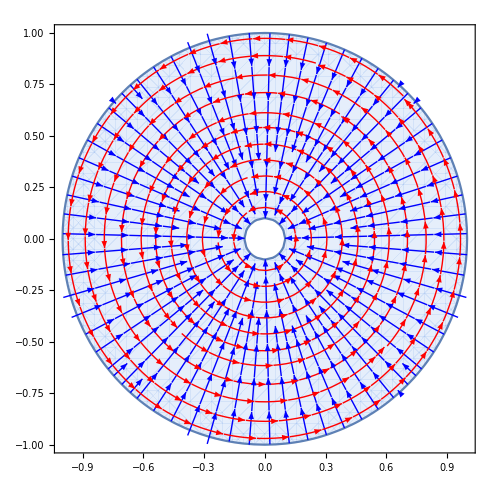

```mathematica
q=-1;
w[z_]=q/2/π*(Log[z]);
ϕ[z_]=D[w[z],z];
ψ[z_]=I*D[w[z],z];
StreamPlot[{ {Re[ϕ[x+I y]],-Im[ϕ[x+I y]]},{Re[ψ[x+I y]],-Im[ψ[x+I y]]}},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0.01<=x^2+y^2≤1],StreamColorFunction->None,StreamStyle->{Blue,Red}]
```

```mathematica
(*Задание 1.2*)
```

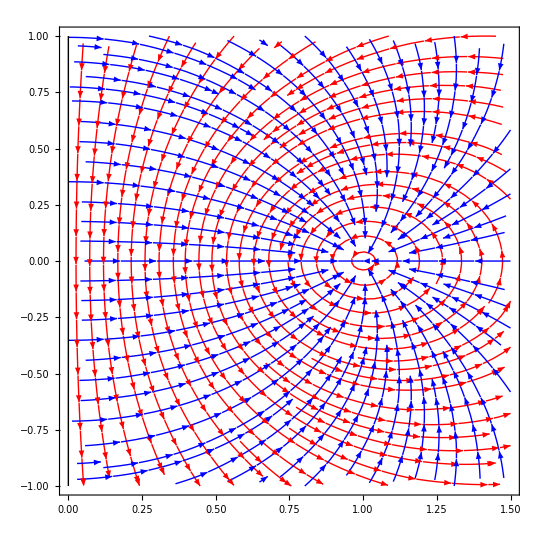

```mathematica
q=-1;
w[z_]=q/2/π*(Log[z-1]-Log[z+1]);
ψ[z_]=D[w[z],z];
ϕ[z_]=I*D[w[z],z];
pl1=StreamPlot[{ {Re[ϕ[x+I y]],-Im[ϕ[x+I y]]},{Re[ψ[x+I y]],-Im[ψ[x+I y]]}},{x,0,1.5},{y,-1,1},StreamColorFunction->None,StreamStyle->{Red,Blue}];
pl2=Graphics[Line[{{0,-1},{0,1}}]];
Show[pl1,pl2]
```

```mathematica
(*Задание 1.3*)
```

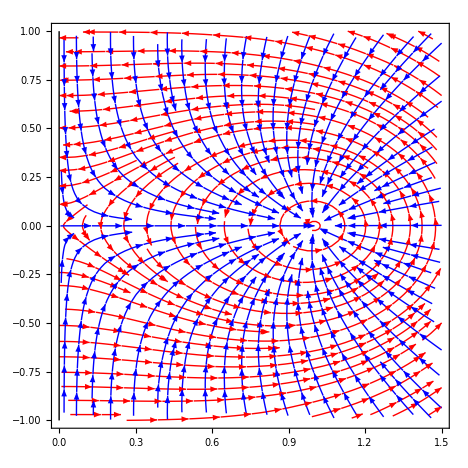

```mathematica
q=-1;
w[z_]=q/2/π*(Log[z-1]+Log[z+1]);
ψ[z_]=D[w[z],z];
ϕ[z_]=I*D[w[z],z];
pl1=StreamPlot[{ {Re[ϕ[x+I y]],-Im[ϕ[x+I y]]},{Re[ψ[x+I y]],-Im[ψ[x+I y]]}},{x,0,1.5},{y,-1,1},StreamColorFunction->None,StreamStyle->{Red,Blue}];
pl2=Graphics[Line[{{0,-1},{0,1}}]];
Show[pl1,pl2]
```

```mathematica
(*Задание 1.4*)
```

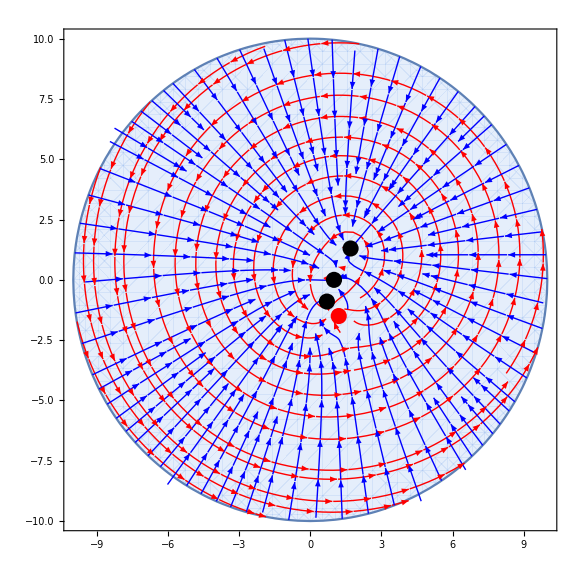

```mathematica
q=-1;
point1=1;
point2=0.7-0.9*I;
point3=1.2-1.5*I;
point4=1.7+1.3*I;
w[z_]=q/2/π*(Log[z-point1]+Log[z-point2]-Log[z-point3]+Log[z-point4]);
ψ[z_]=D[w[z],z];
ϕ[z_]=I*D[w[z],z];
pl1=StreamPlot[{ {Re[ϕ[x+I y]],-Im[ϕ[x+I y]]},{Re[ψ[x+I y]],-Im[ψ[x+I y]]}},{x,-10,10},{y,-10,10},RegionFunction->Function[{x,y},x^2+y^2≤100],StreamColorFunction->None,StreamStyle->{Red,Blue}];
p1=Graphics[{PointSize[0.02],Black,Point[{Re[point1],Im[point1]}]}];
p2=Graphics[{PointSize[0.02],Black,Point[{Re[point2],Im[point2]}]}];
p3=Graphics[{PointSize[0.02],Red,Point[{Re[point3],Im[point3]}]}];
p4=Graphics[{PointSize[0.02],Black,Point[{Re[point4],Im[point4]}]}];
Show[pl1,p1,p2,p3,p4]
```

```mathematica
(*Задание 2*)
```

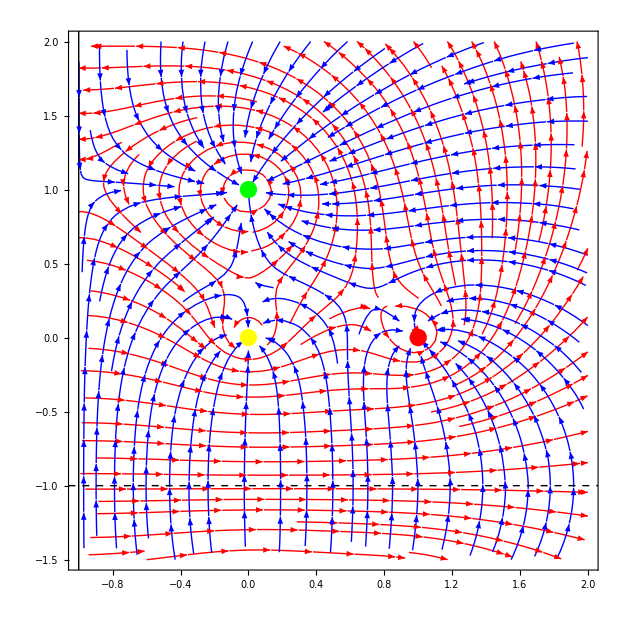

```mathematica
q=-1;
point1=0;
point2=1;
point3=I;
w[z_]=q/2/π*(Log[z-point1]+Log[z-point2]+Log[z-point3]+Log[z-(-1-(1+Re[point1])+Im[point1]I)]+Log[z-(-1-(1+Re[point2])+Im[point2]I)]+Log[z-(-1-(1+Re[point3])+Im[point3]I)]-Log[z-(-I-(I+Im[point1]I)+Re[point1])]-Log[z-(-I-(I+Im[point2]I)+Re[point2])]-Log[z-(-I-(I+Im[point3]I)+Re[point3])]-Log[z-(-I-(I+Im[point1]I)-1-(1+Re[point1]))]-Log[z-(-I-(I+Im[point2]I)-1-(1+Re[point2]))]-Log[z-(-I-(I+Im[point3]I)-1-(1+Re[point3]))]);
ψ[z_]=D[w[z],z];
ϕ[z_]=I*D[w[z],z];
pl1=StreamPlot[{ {Re[ϕ[x+I y]],-Im[ϕ[x+I y]]},{Re[ψ[x+I y]],-Im[ψ[x+I y]]}},{x,-1,2},{y,-1.5,2},StreamColorFunction->None,StreamStyle->{Red,Blue}];
line1=Graphics[Line[{{-1,-2},{-1,3}}]];
line2=Graphics[{Dashed,Line[{{-2,-1},{3,-1}}]}];
p1=Graphics[{PointSize[0.02],Yellow,Point[{Re[point1],Im[point1]}]}];
p2=Graphics[{PointSize[0.02],Red,Point[{Re[point2],Im[point2]}]}];
p3=Graphics[{PointSize[0.02],Green,Point[{Re[point3],Im[point3]}]}];
Show[pl1,line1,line2,p1,p2,p3]
```

```mathematica
(*Задание 3*)
```

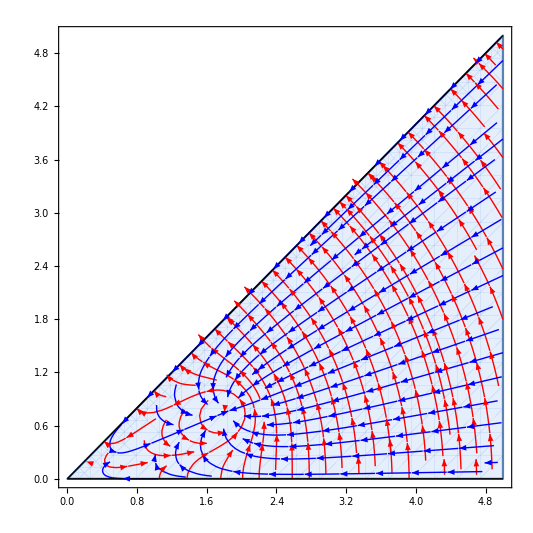

```mathematica
q=-1;
w[z_]=q/2/π*(Log[z-2*(Cos[π/8]+I*Sin[π/8])]+Log[z-2*(Cos[-π/8]+I*Sin[-π/8])]+Log[z-2*(Cos[3*π/8]+I*Sin[3*π/8])]+Log[z-2*(Cos[-3*π/8]+I*Sin[-3*π/8])]+Log[z-2*(Cos[5*π/8]+I*Sin[5*π/8])]+Log[z-2*(Cos[-5*π/8]+I*Sin[-5*π/8])]+Log[z-2*(Cos[7*π/8]+I*Sin[7*π/8])]+Log[z-2*(Cos[-7*π/8]+I*Sin[-7*π/8])]);
ψ[z_]=D[w[z],z];
ϕ[z_]=I*D[w[z],z];
pl1=StreamPlot[{ {Re[ϕ[x+I y]],-Im[ϕ[x+I y]]},{Re[ψ[x+I y]],-Im[ψ[x+I y]]}},{x,0,5},{y,0,5},RegionFunction->Function[{x,y},x>y],StreamColorFunction->None,StreamStyle->{Red,Blue}];
line1=Graphics[Line[{{0,0},{5,0}}]];
line2=Graphics[Line[{{0,0},{5,5}}]];
Show[pl1, line1, line2]
```

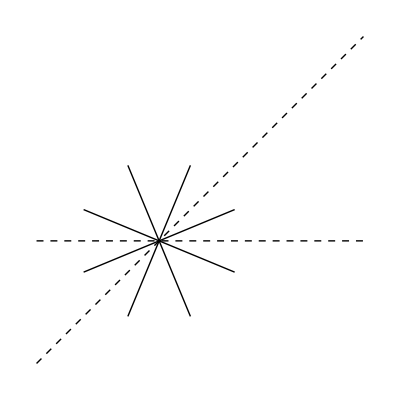

```mathematica
line1=Graphics[Line[{{0,0},2{Cos[π/8],Sin[π/8]}}]];
line2=Graphics[Line[{{0,0},2{Cos[3π/8],Sin[3π/8]}}]];
line3=Graphics[Line[{{0,0},2{Cos[5π/8],Sin[5π/8]}}]];
line4=Graphics[Line[{{0,0},2{Cos[7π/8],Sin[7π/8]}}]];
line5=Graphics[Line[{{0,0},2{Cos[-π/8],Sin[-π/8]}}]];
line6=Graphics[Line[{{0,0},2{Cos[-3π/8],Sin[-3π/8]}}]];
line7=Graphics[Line[{{0,0},2{Cos[-5π/8],Sin[-5π/8]}}]];
line8=Graphics[Line[{{0,0},2{Cos[-7π/8],Sin[-7π/8]}}]];
line9=Graphics[{Dashed,Line[{{-3,0},{5,0}}]}];
line10=Graphics[{Dashed,Line[{{-3,-3},{5,5}}]}];
Show[line1, line2,line3, line4,line5, line6,line7, line8,line9, line10]
```